```mathematica
EdgeList[allGraphs5[K5Key,"graph"]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

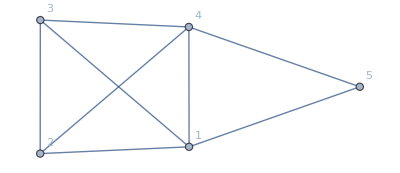

```mathematica
Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,4<->5},VertexLabels->"Name"]
```

```mathematica
Map[EdgeQ[allGraphs5[#,"graph"],#],1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,4<->5]
```

```mathematica
With[{key=1},Fold[And,Map[EdgeQ[allGraphs5[key,"graph"],#],1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,4<->5]]&&Fold[And,Map[EdgeQ[allGraphs5[key,"graph"],#]1,1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,4<->5]]]
```

Map::nonopt: Options expected (instead of 4<->5) beyond position 3 in Map[False,1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,4<->5]. An option must be a rule or a list of rules.

False

```mathematica
keys=Select[Keys[allGraphs5],With[{key=#},IsomorphicGraphQ[Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,4<->5}],allGraphs5[#,"graph"]]&&Fold[And,Map[EdgeQ[allGraphs5[key,"graph"],#]&,{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,4<->5}]]]&]
```

{29440}

```mathematica
ShowGraph5Least[29440]
```

-Graphics-294400

```mathematica
Table[ShowGraph5Least[k]<->(allGraphs5[k,"colofour"]/.RepGraph["C"]),{k,keys}]//TableForm
```

-Graphics-294400<->-Graphics-296080+-Graphics-296050+-Graphics-295270+-Graphics-295240

```mathematica
Table[ShowGraph5Least[k],{k,keys}]
```

{-Graphics-295200,-Graphics-295140,-Graphics-295120,-Graphics-294960,-Graphics-294940,-Graphics-294420,-Graphics-294340,-Graphics-294160,-Graphics-292780,-Graphics-292720,-Graphics-292540,-Graphics-292000,-Graphics-287940,-Graphics-287920,-Graphics-287680,-Graphics-273360,-Graphics-273280,-Graphics-272560,-Graphics-266080,-Graphics-229600,-Graphics-229540,-Graphics-227200,-Graphics-222340,-Graphics-207760,-Graphics-98140,-Graphics-97600,-Graphics-95980,-Graphics-91120,-Graphics-76540,-Graphics-32800}

```mathematica
allGraphs5[20776,"colofour"]/.RepGraph["C"]
```

-Graphics-360850+-Graphics-317110+-Graphics-295240

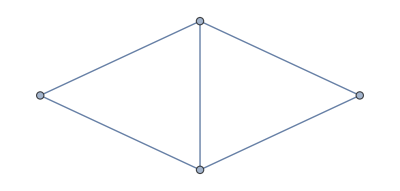

```mathematica
Graph[{1<->2,1<->3,1<->4,2<->3,2<->4}]
```

```mathematica
keys2=Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->4}],allGraphs5[#,"graph"]]&]
```

{28755,28683,28521,27243,27219,27003,26577,26517,22707,22681,22627,22203,21979,20685,20521,9489,9487,9481,9081,8761,7563,7303,3025,2929,363,361,355,337,283,121}

```mathematica
Table[ShowGraph5Least[k],{k,keys2}]
```

{-Graphics-287553,-Graphics-286833,-Graphics-285213,-Graphics-272432,-Graphics-272193,-Graphics-270033,-Graphics-265772,-Graphics-265173,-Graphics-227073,-Graphics-226813,-Graphics-226272,-Graphics-222033,-Graphics-219793,-Graphics-206853,-Graphics-205213,-Graphics-94893,-Graphics-94873,-Graphics-94813,-Graphics-90813,-Graphics-87613,-Graphics-75633,-Graphics-73033,-Graphics-30253,-Graphics-29292,-Graphics-3633,-Graphics-3613,-Graphics-3553,-Graphics-3372,-Graphics-2833,-Graphics-1213}

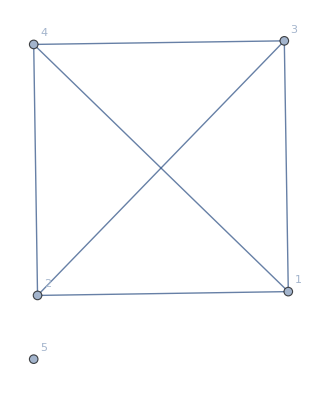

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4},VertexLabels->"Name"]
```

```mathematica
keys3=Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4},VertexLabels->"Name"],allGraphs5[#,"graph"]]&]
```

{28764,27246,22708,9490,364}

```mathematica
Table[(allGraphs5[k,"colofour"]/.RepGraph["C"]),{k,keys3}]
```

{-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295250+-Graphics-295240,-Graphics-360850+-Graphics-297670+-Graphics-295330+-Graphics-295270+-Graphics-295240,-Graphics-492070+-Graphics-297670+-Graphics-296050+-Graphics-295510+-Graphics-295240,-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-302530+-Graphics-295240}

```mathematica
Table[ShowGraph5Least[k]<->(allGraphs5[k,"colofour"]/.RepGraph["C"]),{k,keys2}]
```

{-Graphics-287553<->-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-286833<->-Graphics-303340+-Graphics-296330+-Graphics-296080+-Graphics-296050+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-285213<->-Graphics-304961+-Graphics-297970+-Graphics-297681+-Graphics-297670+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-272432<->-Graphics-295371+-Graphics-317140+-Graphics-296080+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-272193<->-Graphics-296330+-Graphics-317380+-Graphics-295600+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295510+-Graphics-295250+-Graphics-295240,-Graphics-270033<->-Graphics-319540+-Graphics-298571+-Graphics-297681+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295250+-Graphics-295240,-Graphics-265772<->-Graphics-324411+-Graphics-317380+-Graphics-317140+-Graphics-317110+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-265173<->-Graphics-324411+-Graphics-303340+-Graphics-302621+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295250+-Graphics-295240,-Graphics-227073<->-Graphics-360860+-Graphics-297681+-Graphics-295371+-Graphics-360850+-Graphics-297670+-Graphics-295330+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-226813<->-Graphics-297970+-Graphics-361120+-Graphics-295600+-Graphics-360850+-Graphics-297670+-Graphics-295330+-Graphics-295510+-Graphics-295270+-Graphics-295240,-Graphics-226272<->-Graphics-298571+-Graphics-361660+-Graphics-296080+-Graphics-360850+-Graphics-297670+-Graphics-296050+-Graphics-295330+-Graphics-295270+-Graphics-295240,-Graphics-222033<->-Graphics-368170+-Graphics-361120+-Graphics-360860+-Graphics-360850+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-219793<->-Graphics-368170+-Graphics-304961+-Graphics-302621+-Graphics-360850+-Graphics-297670+-Graphics-295330+-Graphics-302530+-Graphics-295270+-Graphics-295240,-Graphics-206853<->-Graphics-382810+-Graphics-361660+-Graphics-360860+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295250+-Graphics-295240,-Graphics-205213<->-Graphics-382810+-Graphics-319540+-Graphics-317140+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-295330+-Graphics-295270+-Graphics-295240,-Graphics-94893<->-Graphics-492081+-Graphics-297681+-Graphics-296330+-Graphics-492070+-Graphics-297670+-Graphics-296050+-Graphics-295510+-Graphics-295250+-Graphics-295240,-Graphics-94873<->-Graphics-492100+-Graphics-297970+-Graphics-296080+-Graphics-492070+-Graphics-297670+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,-Graphics-94813<->-Graphics-492161+-Graphics-298571+-Graphics-295600+-Graphics-492070+-Graphics-297670+-Graphics-296050+-Graphics-295330+-Graphics-295510+-Graphics-295240,-Graphics-90813<->-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-492070+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+-Graphics-295240,-Graphics-87613<->-Graphics-499631+-Graphics-304961+-Graphics-303340+-Graphics-492070+-Graphics-297670+-Graphics-296050+-Graphics-302530+-Graphics-295510+-Graphics-295240,-Graphics-75633<->-Graphics-514750+-Graphics-492161+-Graphics-492081+-Graphics-492070+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295250+-Graphics-295240,-Graphics-73033<->-Graphics-514750+-Graphics-319540+-Graphics-317380+-Graphics-492070+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240,-Graphics-30253<->-Graphics-560111+-Graphics-492161+-Graphics-492100+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-295330+-Graphics-295270+-Graphics-295240,-Graphics-29292<->-Graphics-560111+-Graphics-361660+-Graphics-361120+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-296050+-Graphics-295510+-Graphics-295240,-Graphics-3633<->-Graphics-492081+-Graphics-360860+-Graphics-324411+-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-302530+-Graphics-295250+-Graphics-295240,-Graphics-3613<->-Graphics-492100+-Graphics-368170+-Graphics-317140+-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-302530+-Graphics-295270+-Graphics-295240,-Graphics-3553<->-Graphics-492161+-Graphics-382810+-Graphics-302621+-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-295330+-Graphics-302530+-Graphics-295240,-Graphics-3372<->-Graphics-499631+-Graphics-361120+-Graphics-317380+-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-302530+-Graphics-295510+-Graphics-295240,-Graphics-2833<->-Graphics-514750+-Graphics-361660+-Graphics-303340+-Graphics-492070+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-302530+-Graphics-295240,-Graphics-1213<->-Graphics-560111+-Graphics-319540+-Graphics-304961+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-302530+-Graphics-295240}